```mathematica
stepStieltjes[z_, β_, k_][prev_]:=-1/(z - NIntegrate[x^(k-2)/(1 + β*x^(k-2)*prev)*Exp[-x^2/2]/Sqrt[2Pi], {x, -10, 10}])
```

```mathematica
Im[Nest[stepStieltjes[0.1+0.000001I, 1, 4], 2+10I, 100]]/Pi
```

1.14674

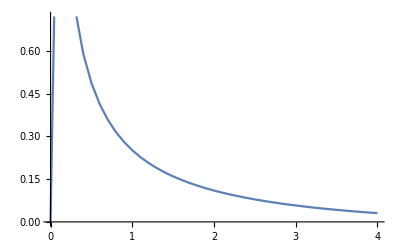

```mathematica
Transpose[
{#,Im[Nest[stepStieltjes[##+0.0001I,1/2, 4], 1+I, 100]]/Pi&/@#}&@Range[0, 4, 0.1] 
]//ListLinePlot
```

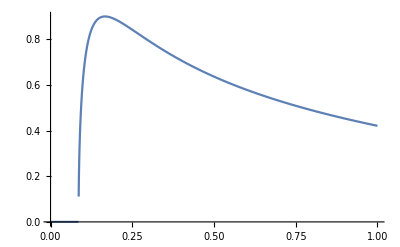

```mathematica
Plot[PDF[MarchenkoPasturDistribution[1/2],x],{x,0,1}]
```

```mathematica
stiel[β_][z_]:=Solve[z*m^3 + (1-β)*m^2 - z*m - 1==0 && Im[m]>0.01, m]
```

```mathematica
Im[m]/Pi/.stiel[1][-2+0.001I]
```

{0.0809985}

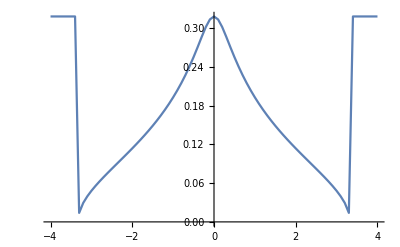

```mathematica
Transpose[{#,First@(Im[m]/Pi/.stiel[2][##+0.0001I])&/@#}&@Range[-4, 4, 0.1]]//ListLinePlot
```

```mathematica
stepStieltjesSample[z_, β_, k_, α_][prev_]:=-1/(z - Mean[#^(k-2)/(1 + β*#^(k-2)*prev)&/@α])
```

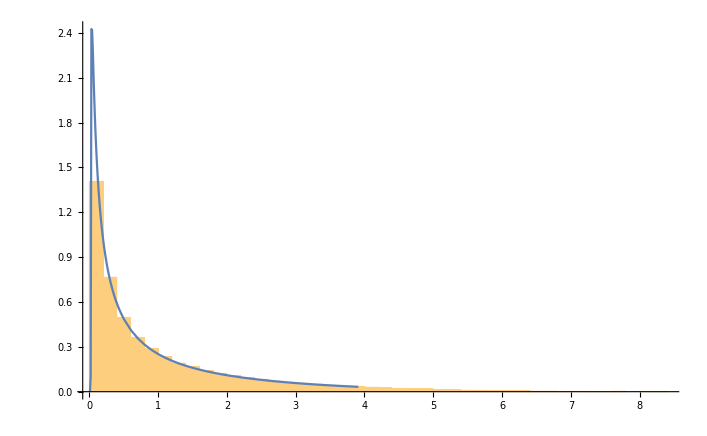

```mathematica
β =1/2;
k = 4;
n=10000;
d = Floor[n*β];
X = RandomVariate[NormalDistribution[], {d, n}];
T = DiagonalMatrix[RandomVariate[NormalDistribution[],n]^(k-2)];
A = X.T.Transpose[X]/n;
p1=Histogram[Eigenvalues[A], Automatic, "PDF"];
dens =Transpose[
{#,Im[Nest[stepStieltjes[##+0.0001I,β, k], 1+I, 100]]/Pi&/@#}&@Join[Range[0, 0.5, 0.01],Range[0.51, 4, 0.1]] 
];
p2=ListLinePlot[dens];
Show[p1, p2, PlotRange->All]
```

```mathematica
dens =Transpose[
{#,Im[Nest[stepStieltjes[##+0.0001I,1/2, 4], 1+I, 100]]/Pi&/@#}&@Join[Range[0, 0.5, 0.01],Range[0.51, 4, 0.1]] 
]
```

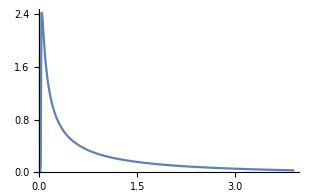

```mathematica
p2=ListLinePlot[dens, PlotRange->All]
```

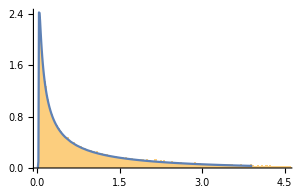

```mathematica
Show[p1, p2]
```

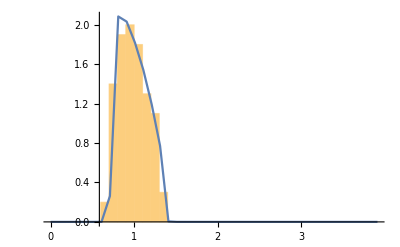

```mathematica
Show[p1, p2, PlotRange->All]
```

```mathematica
stepStieltjesSample[z_, β_, k_, α_][prev_]:=-1/(z - Mean[#^(k-2)/(1 + β*#^(k-2)*prev)&/@α])
```

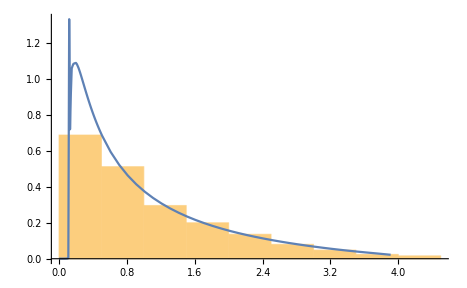

```mathematica
β =1/4;
k = 4;
n=1000;
d = Floor[n*β];
α=RandomVariate[NormalDistribution[0,1], n];
X = RandomVariate[NormalDistribution[], {d, n}];
T = DiagonalMatrix[α^(k-2)];
A = X.T.Transpose[X]/n;
p1=Histogram[Eigenvalues[A], Automatic, "PDF"];
dens =Transpose[
{#,Im[Nest[stepStieltjesSample[##+0.0001I,β, k, α], 1+I, 100]]/Pi&/@#}&@Join[Range[0, 0.5, 0.01],Range[0.51, 4, 0.1]] 
];
p2=ListLinePlot[dens];
Show[p1, p2, PlotRange->All]
```

```mathematica
a = α^(k-2);
p=Total[a]^2/Total[a^2];
```

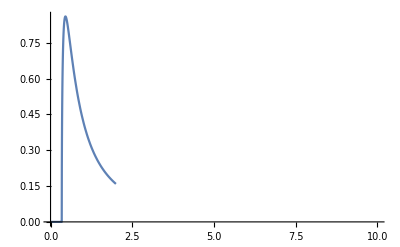

```mathematica
Plot[PDF[MarchenkoPasturDistribution[x/2],x],{x,0,10}]
```